```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/tomikbaikie/Dropbox (Cambridge University)/Physics/Cambridge_Projects_To_Complete/LSC_Singlet_Fission/Data_Figures/IR_PL

```mathematica
names = FileNames["./Data/*.csv"]
files = Import[#]&/@names;
datafiles=files[[;;,;;,{-1,-2}]];
```

{./Data/distance_1_0p5cm_2(v3.0) - (2).csv,./Data/distance_1_0p5cm_2(v3.0).csv,./Data/distance_1_0p5cm(v3.0).csv,./Data/distance_2_0p5cm_2(v3.0).csv,./Data/distance_2_0p5cm(v3.0).csv,./Data/distance_3_0p5cm_2(v3.0).csv,./Data/distance_3_0p5cm(v3.0).csv,./Data/distance_4_0p5cm_2(v3.0).csv,./Data/distance_4_0p5cm(v3.0).csv,./Data/distance_5_0p5cm_2(v3.0).csv,./Data/distance_5_0p5cm(v3.0).csv,./Data/distance_6_0p5cm_2(v3.0).csv,./Data/distance_6_0p5cm(v3.0).csv,./Data/distance_7_0p5cm_2(v3.0).csv,./Data/distance_centre_0p5cm(v3.0).csv,./Data/hitting_back_sample_in_full_power(v3.0).csv,./Data/laser_hitting_back_ofcentre(v3.0).csv,./Data/laser_hitting_back_of_IS(v3.0).csv,./Data/laser(v3.0).csv,./Data/no_laser(v3.0).csv,./Data/test(v3.0).csv}

```mathematica
{names[[2]],names[[4]],names[[6]],names[[8]],names[[10]],names[[12]],names[[14]]}
```

{./Data/distance_1_0p5cm_2(v3.0).csv,./Data/distance_2_0p5cm_2(v3.0).csv,./Data/distance_3_0p5cm_2(v3.0).csv,./Data/distance_4_0p5cm_2(v3.0).csv,./Data/distance_5_0p5cm_2(v3.0).csv,./Data/distance_6_0p5cm_2(v3.0).csv,./Data/distance_7_0p5cm_2(v3.0).csv}

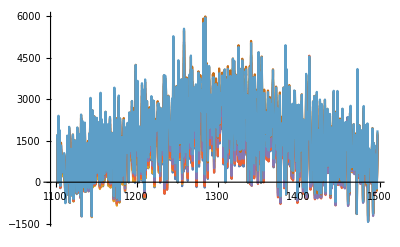

```mathematica
raster = {datafiles[[2]],datafiles[[4]],datafiles[[6]],datafiles[[8]],datafiles[[10]],datafiles[[12]],datafiles[[14]]};
raster = Sort[#]&/@raster;
ListPlot[raster,Joined->True]
```

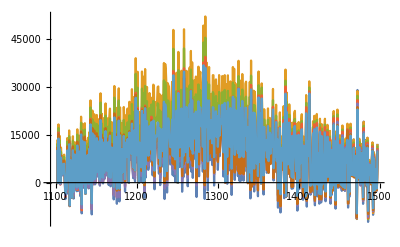

-Graphics-

```mathematica
raster = {datafiles[[3]],datafiles[[5]],datafiles[[7]],datafiles[[9]],datafiles[[11]],datafiles[[13]],datafiles[[15]]};
raster = Sort[#]&/@raster;
ListPlot[raster,Joined->True]
```

{{ampl→544441.,x0→1311.59,sigma→115.49},{ampl→586367.,x0→1314.82,sigma→111.836},{ampl→655730.,x0→1311.6,sigma→109.956},{ampl→595971.,x0→1305.07,sigma→117.811},{ampl→645250.,x0→1301.9,sigma→113.804},{ampl→734706.,x0→1305.05,sigma→109.492},{ampl→734065.,x0→1305.41,sigma→110.761}}

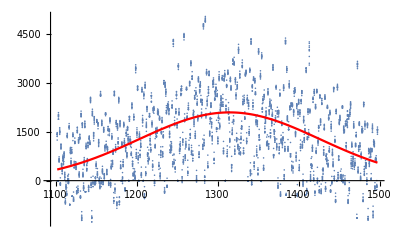

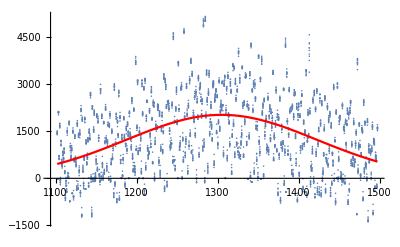

```mathematica
datatofit = raster[[1]];
model[x_]=ampl Evaluate[PDF[NormalDistribution[x0,sigma],x]];

rasterbackground = raster; 
Table[rasterbackground[[i,;;,2]]=rasterbackground[[i,;;,2]]-Min[rasterbackground[[i,;;,2]]],{i,Length[rasterbackground]}];

fits=FindFit[#,model[x],{{ampl,Max[#[[;;,2]]]},{x0,1300},sigma},x]&/@raster

Show[ListPlot[raster[[2]]],Plot[model[x]/. fits[[2]],{x,Min[datatofit[[;;,1]]],Max[datatofit[[;;,1]]]},PlotStyle->Red]]
Show[ListPlot[raster[[4]]],Plot[model[x]/. fits[[4]],{x,Min[datatofit[[;;,1]]],Max[datatofit[[;;,1]]]},PlotStyle->Red]]
```

```mathematica
fit
```

{ampl→734065.,x0→1305.41,sigma→110.761}

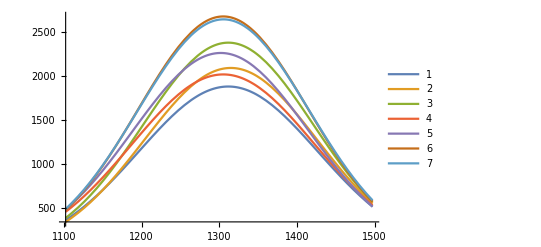

```mathematica
models = model[x]/. fits[[#]]&/@{1,2,3,4,5,6,7};
res=model[y]/. fits[[#]]&/@{1,2,3,4,5,6,7};
Plot[{res[[1]]/.{y->x},res[[2]]/.{y->x},res[[3]]/.{y->x},res[[4]]/.{y->x},res[[5]]/.{y->x},res[[6]]/.{y->x},res[[7]]/.{y->x}},{x,Min[datatofit[[;;,1]]],Max[datatofit[[;;,1]]]},PlotLegends->Automatic]
```

(py Log[(px+√(px^2+py^2))/(-4+px+√((-4+px)^2+py^2))])/(ArcTan[(4-px)/py]+ArcTan[px/py])

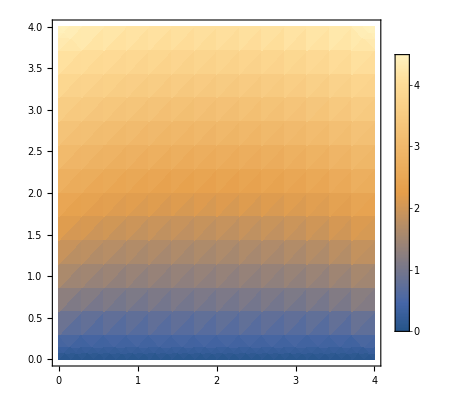

```mathematica
L=4;
edge=Line@{{0,0},{0,L}};
length=RegionMeasure[edge];

(* down *) 

func[px_,py_]=Assuming[0<px<L&&0<py<L&&L>0,Integrate[Sqrt[py^2+(x-px)^2] D[ArcTan[py,x-px],x],{x,0,L}]/Integrate[D[ArcTan[py,x-px],x],{x,0,L}]//FullSimplify]

DensityPlot[func[x,y],{x,0,4},{y,0,4},PlotLegends->Automatic]
```

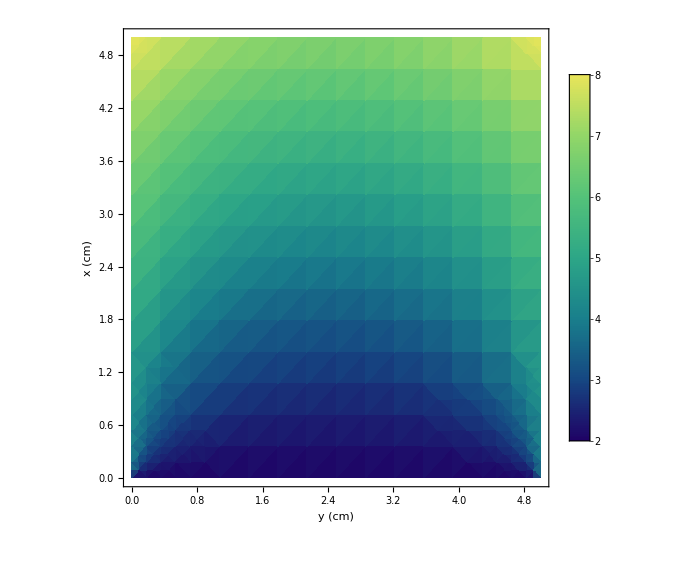

```mathematica
L=5;

angle[dx_,dy_]:=(ArcTan[dx,dy]+ArcTan[dx,L-dy])
(* times two for the fact that theta M is pi/2 (i.e. 90 degrees)*) 
g[dx_,dy_]:=4*(Pi/2)/(angle[dx,dy])

DensityPlot[g[dy,dx],{dx,0,L},{dy,0,L},PlotRange->All,Frame->True,FrameLabel->{Style["y (cm)",Large],Style["x (cm)",Large]},FrameTicksStyle->{{FontSize->16,Orange},{FontSize->16,Green}},ImageSize->Large,ColorFunction->"BlueGreenYellow",PlotLegends->BarLegend[Automatic,LabelStyle->{FontSize->16}]]
```

```mathematica
(*distance from LSC edge, including the gap*) 
distancefromedges = Table[i+0.5,{i,0,4,4/6}]
(*distance from active area *)
distanceactiveedge = Table[i+0.1,{i,0,4,4/5}]
```

{0.5,1.16667,1.83333,2.5,3.16667,3.83333,4.5}

{0.1,0.9,1.7,2.5,3.3,4.1}

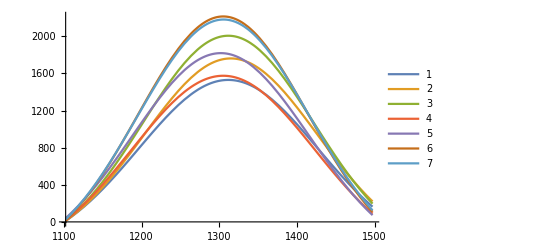

```mathematica
Plot[{(res[[1]]/.{y->x})-(res[[1]]/.{y->1100}),(res[[2]]/.{y->x})-(res[[2]]/.{y->1100}),(res[[3]]/.{y->x})-(res[[3]]/.{y->1100}),(res[[4]]/.{y->x})-(res[[4]]/.{y->1100}),(res[[5]]/.{y->x})-(res[[4]]/.{y->1100}),(res[[6]]/.{y->x})-(res[[6]]/.{y->1100}),(res[[7]]/.{y->x}) -(res[[6]]/.{y->1100})},{x,Min[datatofit[[;;,1]]],Max[datatofit[[;;,1]]]},PlotLegends->Automatic]
```

```mathematica
anglemultiplier = g[#,2.5]&/@distancefromedges
pathlength = func[2.5,#+0]&/@distanceactiveedge
```

{2.28746,2.76995,3.34908,4.,4.70095,5.4362,6.19523}

```mathematica
distanceactiveedge
```

{0.1,0.9,1.7,2.5,3.3,4.1}

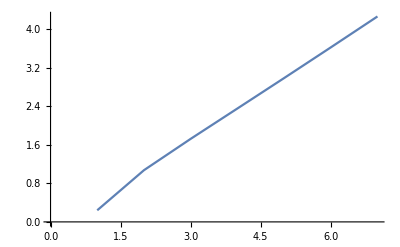

```mathematica
ListPlot[pathlength,Joined->True]
```

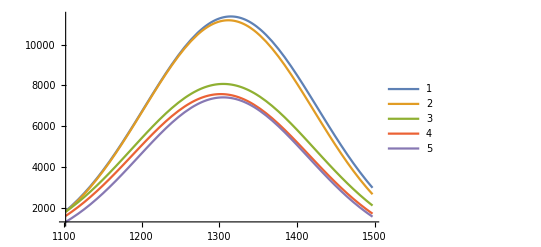

```mathematica
Plot[{anglemultiplier[[6]]*((res[[2]]/.{y->x})),anglemultiplier[[5]]*((res[[3]]/.{y->x})),anglemultiplier[[4]]*((res[[4]]/.{y->x})),anglemultiplier[[3]]*((res[[5]]/.{y->x})),anglemultiplier[[2]]*((res[[6]]/.{y->x}))},{x,Min[datatofit[[;;,1]]],Max[datatofit[[;;,1]]]},PlotLegends->Automatic]
```

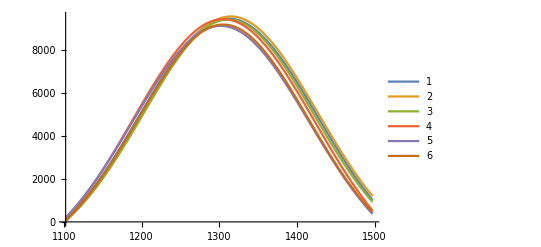

```mathematica
Plot[{anglemultiplier[[7]]*((res[[1]]/.{y->x})-(res[[1]]/.{y->1100})),anglemultiplier[[6]]*((res[[2]]/.{y->x})-(res[[2]]/.{y->1100})),anglemultiplier[[5]]*((res[[3]]/.{y->x})-(res[[3]]/.{y->1100})),1.5*anglemultiplier[[4]]*((res[[4]]/.{y->x})-(res[[4]]/.{y->1100})),1.5*anglemultiplier[[3]]*((res[[5]]/.{y->x})-(res[[4]]/.{y->1100})),1.5*anglemultiplier[[2]]*((res[[6]]/.{y->x})-(res[[6]]/.{y->1100}))},{x,Min[datatofit[[;;,1]]],Max[datatofit[[;;,1]]]},PlotLegends->Automatic]
```

{2.21412×10^6,2.22266×10^6,2.16079×10^6,2.18846×10^6,2.09317×10^6,2.07353×10^6}

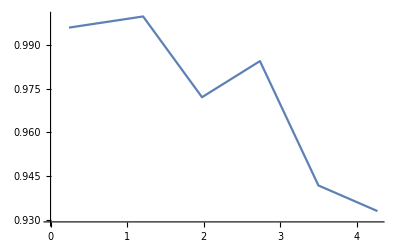

{{0.241009,0.996155},{1.20879,1.},{1.97799,0.972162},{2.73454,0.98461},{3.49779,0.941741},{4.26901,0.932903}}

percentageloss.csv

```mathematica
ints = {NIntegrate[anglemultiplier[[7]]*((res[[1]]/.{y->x})-(res[[1]]/.{y->1100})),{x,Min[datatofit[[;;,1]]],Max[datatofit[[;;,1]]]}],NIntegrate[anglemultiplier[[6]]*((res[[2]]/.{y->x})-(res[[2]]/.{y->1100})),{x,Min[datatofit[[;;,1]]],Max[datatofit[[;;,1]]]}],NIntegrate[anglemultiplier[[5]]*((res[[3]]/.{y->x})-(res[[3]]/.{y->1100})),{x,Min[datatofit[[;;,1]]],Max[datatofit[[;;,1]]]}],NIntegrate[1.5*anglemultiplier[[4]]*((res[[4]]/.{y->x})-(res[[4]]/.{y->1100})),{x,Min[datatofit[[;;,1]]],Max[datatofit[[;;,1]]]}],NIntegrate[1.5*anglemultiplier[[3]]*((res[[5]]/.{y->x})-(res[[4]]/.{y->1100})),{x,Min[datatofit[[;;,1]]],Max[datatofit[[;;,1]]]}],NIntegrate[1.5*anglemultiplier[[2]]*((res[[6]]/.{y->x})-(res[[6]]/.{y->1100})),{x,Min[datatofit[[;;,1]]],Max[datatofit[[;;,1]]]}]}



percentageloss = Transpose[{pathlength,ints}];
percentageloss[[;;,2]]=percentageloss[[;;,2]]/Max[percentageloss[[;;,2]]];
ListPlot[percentageloss,Joined->True]
percentageloss
Export["percentageloss.csv",percentageloss]
```

{2.21412×10^6,2.22266×10^6,2.16079×10^6,2.18846×10^6,2.09317×10^6,2.07353×10^6}

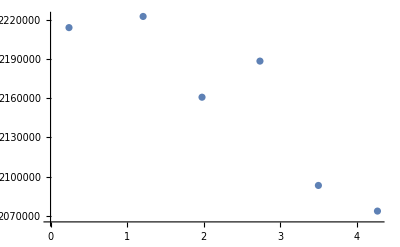

percentageloss.csv

```mathematica
Max[ints]
```

```mathematica
meas2plot =Table[{x, anglemultiplier[[7]]*((res[[1]]/.{y->x})-(res[[1]]/.{y->1100})),anglemultiplier[[6]]*((res[[2]]/.{y->x})-(res[[2]]/.{y->1100})),anglemultiplier[[5]]*((res[[3]]/.{y->x})-(res[[3]]/.{y->1100})),1.5*anglemultiplier[[4]]*((res[[4]]/.{y->x})-(res[[4]]/.{y->1100})),1.5*anglemultiplier[[3]]*((res[[5]]/.{y->x})-(res[[4]]/.{y->1100})),1.5*anglemultiplier[[3]]*((res[[5]]/.{y->x})-(res[[4]]/.{y->1100})),1.5*anglemultiplier[[2]]*((res[[6]]/.{y->x})-(res[[6]]/.{y->1100}))},{x,Min[datatofit[[;;,1]]],Max[datatofit[[;;,1]]]}];

Export["data2plot.csv",meas2plot]
```

data2plot.csv

```mathematica
ListPlot[raster,Joined->True]
```

-Graphics-